Логаш Полина 
Вариант 7

1. Задаём начальные данные :

```mathematica
Subscript[x, 0]=-1;Subscript[x, 1]=6;Subscript[x, 2]=9;Subscript[x, 3]=12;
Subscript[f, 0]=0;Subscript[f, 1]=-20;Subscript[f, 2]=47;Subscript[f, 3]=96;
n=3;
```

2. Формируем линейный интерполяционный сплайн на частичном отрезке [x_k,x_(k+1)]:

```mathematica
Subscript[P, k_][t_]=Subscript[f, k]+(t-Subscript[x, k])*Subscript[A, k];
```

3. Записываем интерполяционные условия в систему линейных уравнений:

```mathematica
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
eq2={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
```

4. Формируем систему линейных уравнений для определения неизвестных коэффициентов сплайна:

```mathematica
eq=Join[eq1,eq2]
```

{7 A_0==-20,-20+3 A_1==47,47+3 A_2==96}

5. Решаем систему линейных уравнений:

```mathematica
koef=Solve[eq,{}]
```

{{A_0→-20/7,A_1→67/3,A_2→49/3}}

6. Строим искомый сплайн:

```mathematica
spl=Table[Subscript[P, k][t]/.koef,{k,0,n-1}]//Expand//Flatten
```

{-20/7-(20 t)/7,-154+(67 t)/3,-100+(49 t)/3}

7. Проверяем интерполяционные условия:

```mathematica
Table[(spl[[k]]//.t->Subscript[x, k-1])==Subscript[f, k-1],{k,1,n}]
(spl[[n]]//.t->Subscript[x, n])==Subscript[f, n]
```

{True,True,True}

True

8. Изображаем исходную систему точек и
полученный интерполяционный сплайн в одной системе координат:

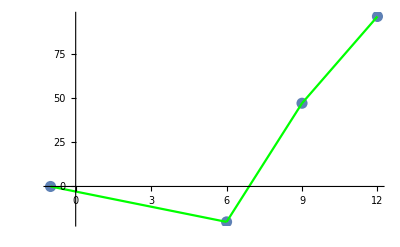

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]}, {i,0,n}],PlotStyle->{PointSize[0.02]}];
Gr2=Table[Plot[spl[[k]],{t,Subscript[x, k-1],Subscript[x, k]},PlotStyle->{Green}],{k,1,n}];
Show[Gr1,Gr2]
```

```mathematica
--------------------------------
```

1. Задаём начальные данные :

```mathematica
Subscript[x, 0]=-1;Subscript[x, 1]=6;Subscript[x, 2]=9;Subscript[x, 3]=12;
Subscript[f, 0]=0;Subscript[f, 1]=-20;Subscript[f, 2]=47;Subscript[f, 3]=96;
n=3;
```

2. Формируем квадратичный интерполяционный сплайн на частичном отрезке [x_k,x_(k+1)]:

```mathematica
Subscript[P, k_][t_]=Subscript[f, k]+(t-Subscript[x, k])*(Subscript[A, k] t+Subscript[B, k]);
```

3. Записываем интерполяционные условия в систему линейных уравнений:

```mathematica
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
Subscript[PP, k_][t_]=D[Subscript[P, k][t], t];
eq2=Table[Subscript[PP, k][Subscript[x, k+1]]==Subscript[PP, k+1][Subscript[x, k+1]],{k,0,n-2}];
eq3={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
```

4. Записываем дополнительные условия согласно поставленной задаче:

```mathematica
eq4={Subscript[PP, n-1][Subscript[x, n]]==0};
```

5. Формируем систему линейных уравнений для определения неизвестных коэффициентов сплайна:

```mathematica
eq=Join[eq1,eq2,eq3,eq4]
```

{7 (6 A_0+B_0)==-20,-20+3 (9 A_1+B_1)==47,13 A_0+B_0==6 A_1+B_1,12 A_1+B_1==9 A_2+B_2,47+3 (12 A_2+B_2)==96,15 A_2+B_2==0}

6. Решаем систему линейных уравнений:

```mathematica
koef=Solve[eq,{}]
```

{{A_0→104/49,A_1→31/9,A_2→-49/9,B_0→-764/49,B_1→-26/3,B_2→245/3}}

7. Строим искомый сплайн:

```mathematica
spl=Table[Subscript[P, k][t]/.koef,{k,0,n-1}]//Expand//Flatten
```

{-764/49-(660 t)/49+(104 t^2)/49,32-(88 t)/3+(31 t^2)/9,-688+(392 t)/3-(49 t^2)/9}

8. Проверяем интерполяционные условия:

```mathematica
Table[(spl[[k]]//.t->Subscript[x, k-1])==Subscript[f, k-1],{k,1,n}]
(spl[[n]]//.t->Subscript[x, n])==Subscript[f, n]
```

{True,True,True}

True

9. Проверяем дополнительное условие:

```mathematica
(D[spl[[n]],{t,1}]//. t->b)==0
```

392/3-(98 b)/9==0

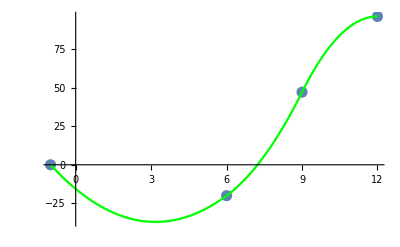

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]}, {i,0,n}], PlotStyle->{PointSize[0.02]}];
Gr3=Table[Plot[spl[[k]],{t,Subscript[x, k-1],Subscript[x, k]},PlotStyle->{Green}],{k,1,n}];
Show[Gr1,Gr3,PlotRange->All]
```

```mathematica
--------------------------------
```

1. Задаём начальные данные :

```mathematica
Subscript[x, 0]=-1;Subscript[x, 1]=6;Subscript[x, 2]=9;Subscript[x, 3]=12;
Subscript[f, 0]=0;Subscript[f, 1]=-20;Subscript[f, 2]=47;Subscript[f, 3]=96;
n=3;
```

2. Формируем rкубический интерполяционный сплайн на частичном отрезке [x_k,x_(k+1)]:

```mathematica
Subscript[P, k_][t_]=Subscript[f, k]+(t-Subscript[x, k])*(Subscript[A, k] t^2+Subscript[B, k] t+Subscript[C, k]);
```

3. Записываем интерполяционные условия в систему линейных уравнений:

```mathematica
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
Subscript[PP, k_][t_]=D[Subscript[P, k][t], t];
eq2=Table[Subscript[PP, k][Subscript[x, k+1]]==Subscript[PP, k+1][Subscript[x, k+1]],{k,0,n-2}];
Subscript[PPP, k_][t_]=D[Subscript[PP, k][t], t];
eq3=Table[Subscript[PPP, k][Subscript[x, k+1]]==Subscript[PPP, k+1][Subscript[x, k+1]],{k,0,n-2}];
eq4={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
```

4. Записываем дополнительные условия согласно поставленной задаче:

```mathematica
eq5={Subscript[PP, n-1][Subscript[x, n]]==0};
eq6={Subscript[PP, 0][Subscript[x, 0]]==0};
```

5. Формируем систему линейных уравнений
для определения неизвестных коэффициентов сплайна:

```mathematica
eq=Join[eq1,eq2,eq3,eq4,eq5,eq6]
```

{7 (36 A_0+6 B_0+C_0)==-20,-20+3 (81 A_1+9 B_1+C_1)==47,36 A_0+6 B_0+7 (12 A_0+B_0)+C_0==36 A_1+6 B_1+C_1,81 A_1+9 B_1+3 (18 A_1+B_1)+C_1==81 A_2+9 B_2+C_2,38 A_0+2 B_0==24 A_1+2 B_1,42 A_1+2 B_1==36 A_2+2 B_2,47+3 (144 A_2+12 B_2+C_2)==96,144 A_2+12 B_2+3 (24 A_2+B_2)+C_2==0,A_0-B_0+C_0==0}

6. Решаем систему линейных уравнений:

```mathematica
koef=Solve[eq,{}]
```

{{A_0→9648/25039,A_1→-8879/13797,A_2→-10667/13797,B_0→-58460/25039,B_1→58448/4599,B_2→20099/1533,C_0→-68108/25039,C_1→-61196/1533,C_2→-15159/511}}

7. Строим искомый сплайн:

```mathematica
spl=Table[Subscript[P, k][t]/.koef,{k,0,n-1}]//Expand//Flatten
```

{-68108/25039-(126568 t)/25039-(48812 t^2)/25039+(9648 t^3)/25039,112172/511-(59364 t)/511+(25402 t^2)/1533-(8879 t^3)/13797,160448/511-(75456 t)/511+(30766 t^2)/1533-(10667 t^3)/13797}

8. Проверяем интерполяционные условия:

```mathematica
Table[(spl[[k]]//.t->Subscript[x, k-1])==Subscript[f, k-1],{k,1,n}]
(spl[[n]]//.t->Subscript[x, n])==Subscript[f, n]
```

{True,True,True}

True

9. Проверяем дополнительные условия:

```mathematica
(D[spl[[n]],{t,1}]//.t->b)==0
(D[spl[[1]],{t,2}]//.t->a)==0
```

-75456/511+(61532 b)/1533-(10667 b^2)/4599==0

-97624/25039+(57888 a)/25039==0

10. Изображаем исходную систему точек и
полученный интерполяционный сплайн в одной системе координат:

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}],PlotStyle->{PointSize[0.02]}];
Gr4=Table[Plot[spl[[k]],{t,Subscript[x, k-1],Subscript[x, k]},PlotStyle->Blue],{k,1,n}];
```

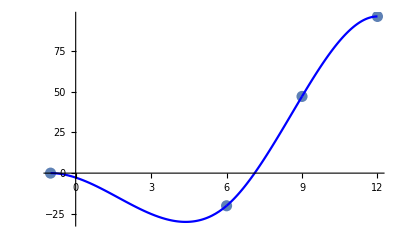

```mathematica
Show[Gr1,Gr4,PlotRange->All]
```

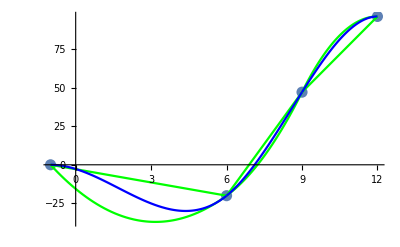

```mathematica
Show[Gr1,Gr2,Gr3,Gr4,PlotRange->All]
```